```mathematica
ClearAll["Global`*"]
```

```mathematica
(*eletromagnetico 6Dz0 k0{r+,ωi}*)
ListPlot[{{0.1,0.2110},{0.3,0.6224},{0.5,1.0289},{0.6,1.2321},{0.8,1.6388},{1,2.0904},{5,5.9230},{10,10.9564},{50,50.9902},{100,100.9905073700}},PlotStyle->{Blue,PointSize[0.02]},PlotRange->All,Frame-> True,FrameLabel->{"r_+","-ω_I"},LabelStyle->Directive[Large],PlotLegends->Placed[ {"κ=0"},{After,Center}]]
```

-Graphics-

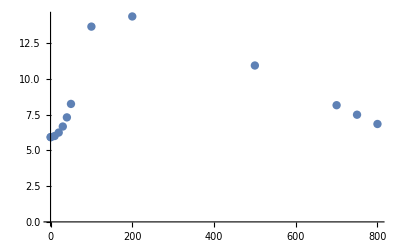

{a→0.000773608,b→5.99483}

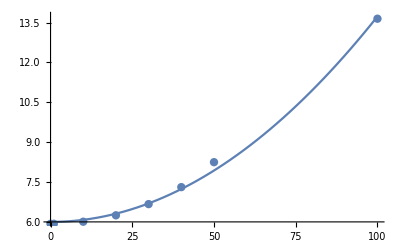

```mathematica
(*eletromagnetico 6Dz0 r+5 {k,ωi}*)
r5=ListPlot[{{0,5.9230},{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463},{200,14.3559},{500,10.9289},{700,8.1548},{750,7.48996},{800,6.84161}},PlotStyle-> PointSize[0.015],PlotRange->All]
x5={{0,5.9230},{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463}};
FindFit[x5,a x^2+b,{a,b},x]
rx5=Plot[0.0007736076708237989 x^2+5.9948259368200345,{x,0,100}];
Show[{rx5},r5]
```

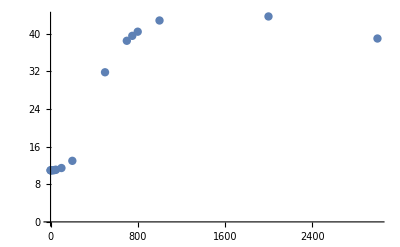

{a→0.0000833412,b→10.7715}

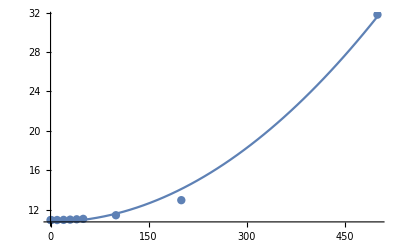

```mathematica
(*eletromagnetico 6Dz0 r+10 {k,ωi}*)
r10=ListPlot[{{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913},{700,38.4831},{750,39.5315},{800,40.4138},{1000,42.7942},{2000,43.6513},{3000,38.9648}},PlotStyle-> PointSize[0.015],PlotRange->All]
x10={{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913}};
FindFit[x10,a x^2+b,{a,b},x]
rx10=Plot[0.0000833412355120511 x^2+10.77148692098328,{x,0,500}];
Show[{rx10},r10]
```

```mathematica
(* r+5 e r+10 JUNTOS*)
r510=ListPlot[{{{0,5.9230},{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463},{200,14.3559},{500,10.9289},{700,8.1548},{750,7.48996},{800,6.84161}},{{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913},{700,38.4831},{750,39.5315},{800,40.4138},{1000,42.7942},{2000,43.6513},{3000,38.9648}}},PlotRange->All,PlotStyle->{{Red,PointSize[0.02]},{Blue,PointSize[0.02]}},PlotRange->All,Frame-> True,FrameLabel->{"κ","-ω_I"},LabelStyle->Directive[Large],PlotLegends->Placed[ {"r_+=5","r_+=10"},{After,Center}]]
Show[{r510,rx5,rx10}]
```

-Graphics-

-Graphics-

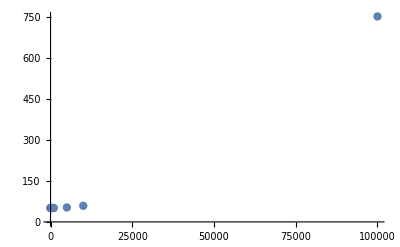

{a→7.02133×10^-8,b→51.1017}

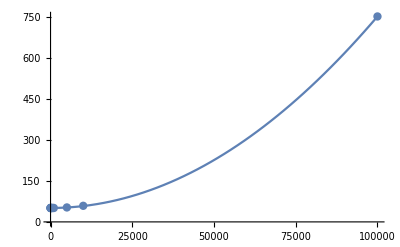

```mathematica
(*eletromagnetico 6Dz0 r+50 {k,ωi}*)
r50=ListPlot[{{0,50.990290428662},{1,50.9902090507946},{10,50.990298357079},{50,50.9904},{100,50.9910},{200,50.9934},{500,51.0101117756},{700,51.0291},{1000,51.0695},{5000,52.9754569336},{10000,59.0000},{100000,753.2260421}},PlotStyle-> PointSize[0.015],PlotRange->All]
x50={{0,50.990290428662},{1,50.9902090507946},{10,50.990298357079},{50,50.9904},{100,50.9910},{200,50.9934},{500,51.0101117756},{700,51.0291},{1000,51.0695},{5000,52.9754569336},{10000,59.0000},{100000,753.2260421}};
FindFit[x50,a x^2+b,{a,b},x]
rx50=Plot[7.021334362837382/10^8 x^2+51.101653324870746,{x,0,100000}];
Show[{rx50},r50]
```

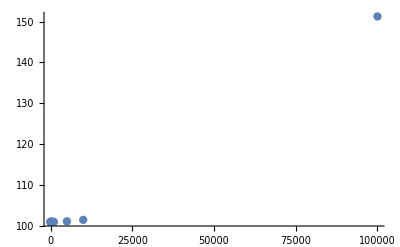

{a→5.02641×10^-9,b→100.993}

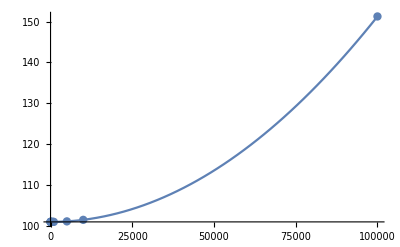

```mathematica
(*eletromagnetico 6Dz0 r+100 {k,ωi}*)
r100=ListPlot[{{0,100.9905073700},{1,100.9905073782},{10,100.9905074275},{50,100.9950},{100,100.995123541},{200,100.995272830236},{500,100.996317861166},{700,100.997512188688},{1000,101.000050126},{5000,101.119485429878},{10000,101.492756983},{100000,151.257353411}},PlotStyle-> PointSize[0.015],PlotRange->All]
x100={{0,100.9905073700},{1,100.9905073782},{10,100.9905074275},{50,100.9950},{100,100.995123541},{200,100.995272830236},{500,100.996317861166},{700,100.997512188688},{1000,101.000050126},{5000,101.119485429878},{10000,101.492756983},{100000,151.257353411}};
FindFit[x100,a x^2+b,{a,b},x]
rx100=Plot[5.026407296008313/10^9 x^2+100.99325086098652,{x,0,100000}];
Show[{rx100},r100]
```

```mathematica
r50100=ListPlot[{{{0,50.990290428662},{1,50.9902090507946},{10,50.990298357079},{50,50.9904},{100,50.9910},{200,50.9934},{500,51.0101117756},{700,51.0291},{1000,51.0695},{5000,52.9754569336},{10000,59.0000},{100000,753.2260421}},{{0,100.9905073700},{1,100.9905073782},{10,100.9905074275},{50,100.9950},{100,100.995123541},{200,100.995272830236},{500,100.996317861166},{700,100.997512188688},{1000,101.000050126},{5000,101.119485429878},{10000,101.492756983},{100000,151.257353411}}},PlotStyle->{{Red,PointSize[0.02]},{Blue,PointSize[0.02]}},PlotRange->All,Frame-> True,FrameLabel->{"κ","-ω_I"},LabelStyle->Directive[Large],PlotLegends->Placed[ {"r_+=50","r_+=100"},{After,Center}] ]
Show[{r50100,rx50,rx100}]
```

-Graphics-

-Graphics-

```mathematica
tudo=ListPlot[{{{0,5.9230},{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463},{200,14.3559},{500,10.9289},{700,8.1548},{750,7.48996},{800,6.84161}},{{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913},{700,38.4831},{750,39.5315},{800,40.4138},{1000,42.7942},{2000,43.6513},{3000,38.9648}},{{0,50.990290428662},{1,50.9902090507946},{10,50.990298357079},{50,50.9904},{100,50.9910},{200,50.9934},{500,51.0101117756},{700,51.0291},{1000,51.0695},{5000,52.9754569336},{10000,59.0000}},{{0,100.9905073700},{1,100.9905073782},{10,100.9905074275},{50,100.9950},{100,100.995123541},{200,100.995272830236},{500,100.996317861166},{700,100.997512188688},{1000,101.000050126},{5000,101.119485429878},{10000,101.492756983}}},PlotRange->All,PlotStyle->{{Red,PointSize[0.01]},{Blue,PointSize[0.01]},{Black,PointSize[0.01]},{Yellow,PointSize[0.01]}},PlotRange->All,Frame-> True,FrameLabel->{"κ","ω_I"},LabelStyle->Directive[Medium],PlotLegends->Placed[ {"r_+=5","r_+=10","r_+=50","r_+=100"},{After,Center}]]
```

-Graphics-

```mathematica
Show[{tudo,rx5,rx10,rx50,rx100}]
```

-Graphics-